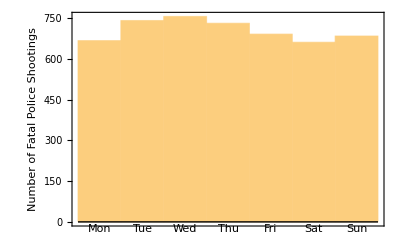

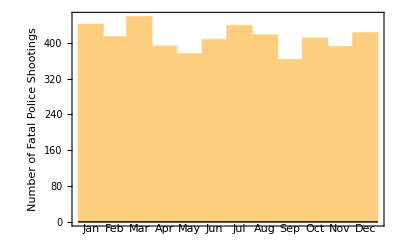

```mathematica
data:=Import["shootingdata.csv"][[2;;4939,3]]
DateHistogram[data,"Day",DateReduction->"Week",Frame->True,FrameLabel->{None,"Number of Fatal Police Shootings"}]
DateHistogram[data,"Month",DateReduction->"Year",Frame->True,FrameLabel->{None,"Number of Fatal Police Shootings"}]
```